Video - igre skozi čas
Analiza videoiger glede na različne lastnosti.

## Pridobivanje podatkov

Podatke sem pridobil iz podatkovne baze Wolfram data repository.

```mathematica
podatki= ResourceData["Video Games Until April 2017"]
```

Dataset[<>]

## Analiza iger glede na žanr, popularnost in oceno

Analiziral bom in narisal nekaj grafov glede na žanr, popularnost ter oceno. Podatki so obdelani in predstavljeni tudi z grafi.

```mathematica
shooters = Length[Select[podatki, MemberQ[#["Genres"], "Shooter"]&]];
```

```mathematica
advent = Length[Select[podatki, MemberQ[#["Genres"], "Adventure"]&]];
```

```mathematica
indie = Length[Select[podatki, MemberQ[#["Genres"], "Indie"]&]];
```

```mathematica
platform = Length[Select[podatki, MemberQ[#["Genres"], "Platform"]&]];
```

```mathematica
sport = Length[Select[podatki, MemberQ[#["Genres"], "Sport"]&]];
```

```mathematica
rpg = Length[Select[podatki, MemberQ[#["Genres"], "Role-playing (RPG)"]&]];
others = Length[podatki] - shooters - advent - indie - platform - sport - rpg
```

9523

```mathematica
PieChart[<|"Shooters"->shooters,"Adventure"->advent,"Indie"->indie,"Platform"->platform, "Sport"-> sport, "RPG" -> rpg, "Others"-> others|>,ChartLabels->Callout[Automatic], PlotLabel->"Popularnost najpogostejših žanrov"]
```

-Graphics-

Kot vidimo so najbolj popularne igre tipa Adventure in sicer zavzemajo skoraj četrtino vseh žanrov.

```mathematica
popularnost = podatki[All, "Popularity"];
```

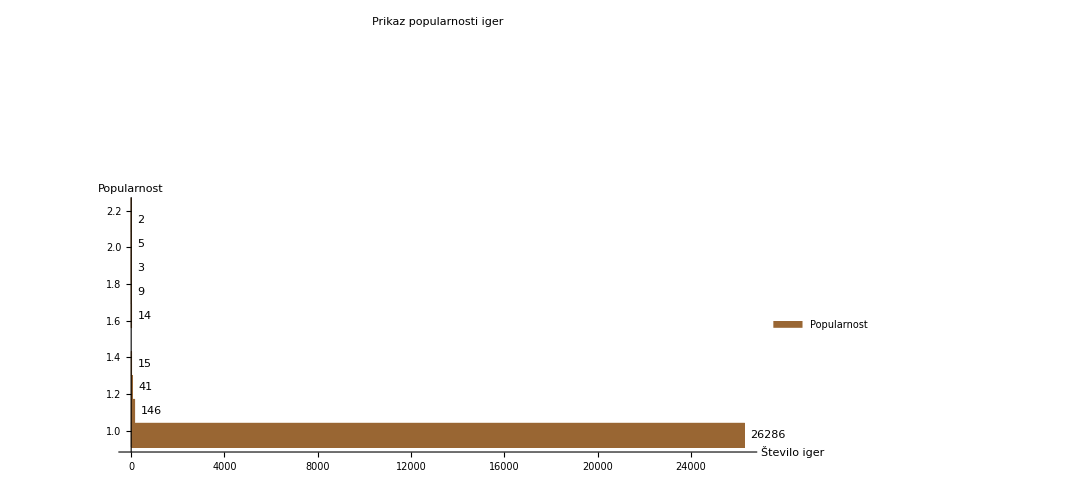

```mathematica
Histogram[popularnost,ChartStyle->Brown, BarOrigin->Left,LabelingFunction->After,ImageSize->{800,550},ChartLegends->{"Popularnost"},PlotLabel->"Prikaz popularnosti iger",AxesLabel->{"Število iger","Popularnost"}, PlotRange->Automatic]
```

```mathematica
topPopular1 = podatki[All, {"Popularity", "Name"}];
topPopular2 = ReverseSort[topPopular1];
topPop = {topPopular2[1], topPopular2[2], topPopular2[3], topPopular2[4]}
```

{,,,}

```mathematica
ocene = podatki[All, "Rating"];
```

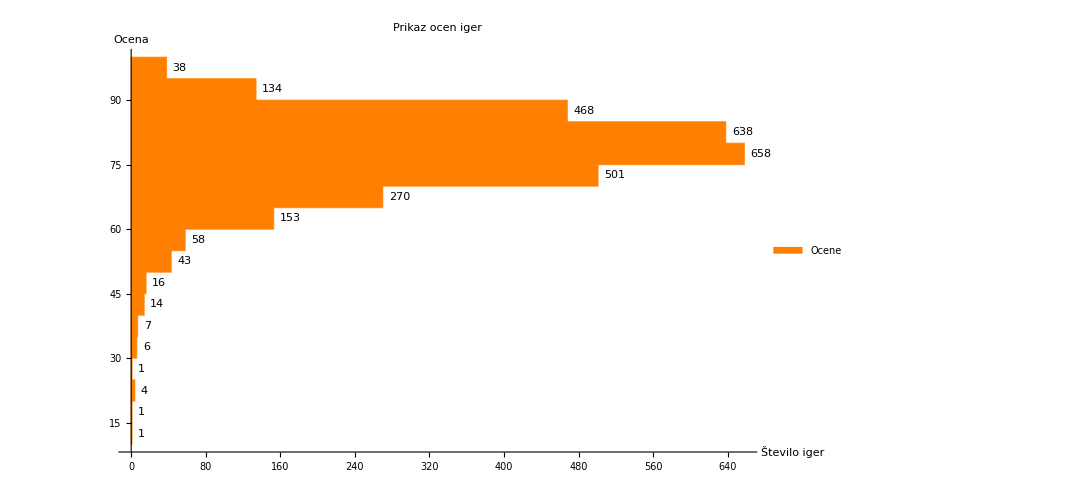

```mathematica
Histogram[ocene,ChartStyle -> Orange, BarOrigin->Left,LabelingFunction->After,ImageSize->{800,550},ChartLegends->{"Ocene"},PlotLabel->"Prikaz ocen iger",AxesLabel->{"Število iger","Ocena"}]
```

Graf popularnosti proti oceni nam kaže, da nerabijo igre biti dobre da so popularne saj je veliko več iger z dobro oceno, kot jih je popularnih.

## Analiza glede na čas

Analizirali bomo večje korporace in koliko iger producirajo letno.

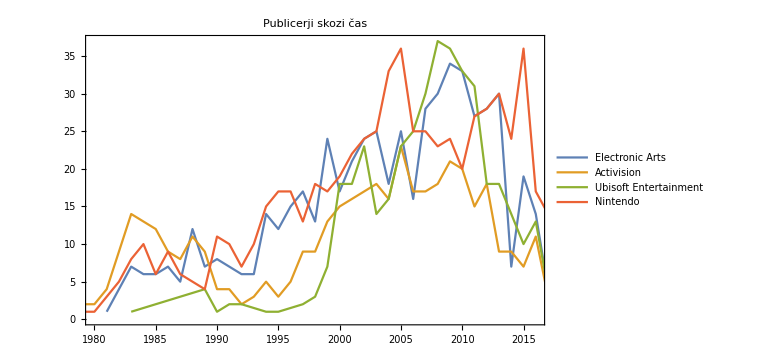

```mathematica
publicerji = Table[Legended[Normal@GroupBy[Select[podatki,MemberQ[#Publishers,p]&&!MissingQ@#@"FirstReleaseDate"&],Normal@DateObject[#@"FirstReleaseDate","Year"]&,Length],p],{p,{"Electronic Arts","Activision","Ubisoft Entertainment", "Nintendo"}}];

DateListPlot[publicerji, PlotLabel->"Publicerji skozi čas", PlotRange->{{{1980}, {2016}}, Automatic}, ImageSize->Large]
```

## Analiza posameznih serij iger

Poglejmo si za primer kako so se spreminjale ocene Super Mariota skozi čas in kakšno bi bilo povprečje njihovih ocen (regresijska premica)

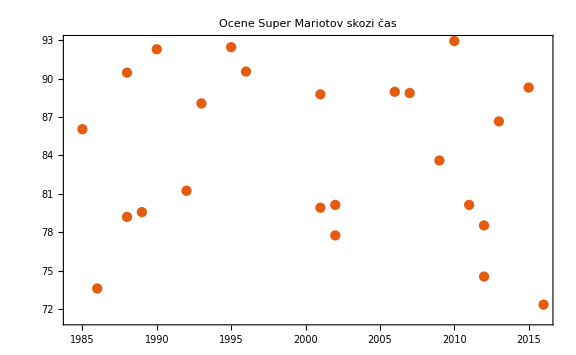

```mathematica
superMario=Select[podatki,#Collection=="Super Mario"&];
sm1 = superMario[All, {"Rating", "FirstReleaseDate"}];
sm2 = sm1[Select[#Rating > 0 &]];
sm3 = {};
sm4={};
Do[
row = sm2[[n]];
date  = DateObject[row[[2]], "Year"][[1]][[1]];
sm3 = Append[sm3, date];
rating = row[[1]];
sm4 = Append[sm4, rating];
, {n, Length[sm2]}
]
sm5 = Sort[Transpose[{sm3, sm4}]];
ListPlot[sm5, PlotLabel->"Ocene Super Mariotov skozi čas", PlotTheme->"Scientific", ImageSize->Large]
```

Iz podatkov se sprva ne vidi ali se kvaliteta Super Mariotov izboljšuje ali morda celo slabša. Naredimo premico, ki se najbolje prilega danim podatkom.

```mathematica
najboljsaPremica =LinearModelFit[sm5, x, x]
```

FittedModel[232.216-0.074082 x]

Prikazemo podatke z regresisko premico

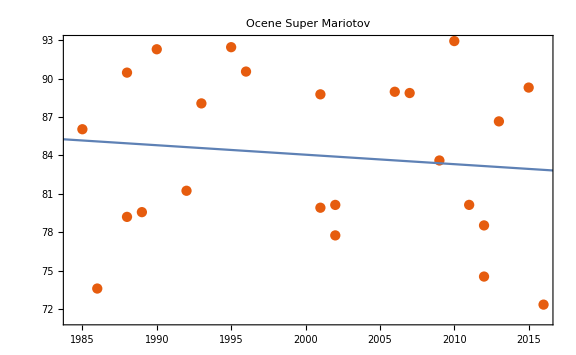

```mathematica
Show[ListPlot[sm5, PlotLabel->"Ocene Super Mariotov", PlotTheme->"Scientific", ImageSize->Large], Plot[najboljsaPremica["BestFit"],{x, 1980, 2017}]]
```

Vidimo, da kvaliteta iger skozi čas pada.

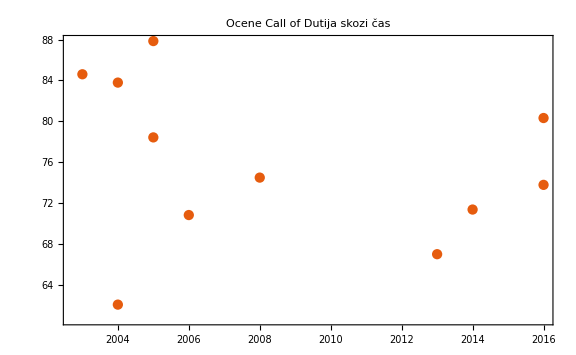

```mathematica
callOfDuty=Select[podatki,#Collection=="Call of Duty"&];
cod1 = callOfDuty[All, {"Rating", "FirstReleaseDate", "Name"}];
cod2 = cod1[Select[#Rating > 0 &]];
cod3 = {};
cod4={};
Do[
row = cod2[[n]];
date  = DateObject[row[[2]], "Year"][[1]][[1]];
cod3 = Append[cod3, date];
rating = row[[1]];
cod4 = Append[cod4, rating];
, {n, Length[cod2]}
]
cod5 = Sort[Transpose[{cod3, cod4}]];
ListPlot[cod5, PlotLabel->"Ocene Call of Dutija skozi čas", PlotTheme->"Scientific", ImageSize->Large]
```

Tukaj sem bolj pričakoval, da bo kavaliteta iger padala, a poglejmo če je res. Tudi se zdi čudno, da ni nobenega vhoda med letom  2008 in 2013, kar pomeni, da kar precej iger ni v naših podatkih.

```mathematica
najboljsaPremica2 = LinearModelFit[cod5, x, x]
```

FittedModel[880.817-0.400761 x]

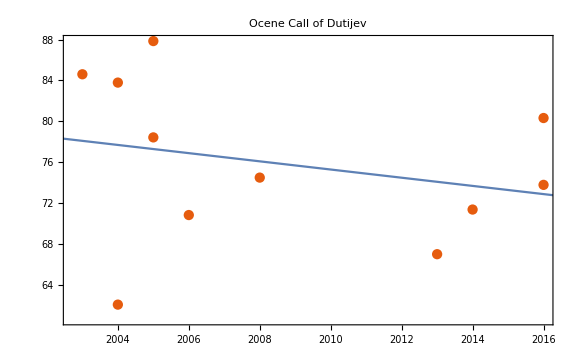

```mathematica
Show[ListPlot[cod5, PlotLabel->"Ocene Call of Dutijev", PlotTheme->"Scientific", ImageSize->Large], Plot[najboljsaPremica2["BestFit"],{x, 1980, 2017}]]
```

Regresijska premica je bolj strma kot v prvem primeru torej vemo, da se kvaliteta CoD-ov še hitreje zmanjšuje

## Aplikacija v oblaku

```mathematica
IskanaIgra[console_] := Select[podatki, MemberQ[#["Platforms"], console] &];
```

```mathematica
iskaniIgralci[igralci_] := Select[podatki, MemberQ[#["GameModes"], igralci] &];
```

```mathematica
conzolaInIgralci[console_, igralci_] := Select[Select[podatki, MemberQ[#["Platforms"], console] &], MemberQ[#["GameModes"], igralci] &];
```

```mathematica
conzolaInIgralci2[console_, igralci_] := ReverseSort[conzolaInIgralci[console, igralci][All, {"Rating", "Name"}] [Select[#Rating > 0 &]]][1 ;; 10];
```

```mathematica
conzolaInIgralc3[console_, igralci_]:= {{conzolaInIgralci2[console, igralci][1][1],conzolaInIgralci2[console, igralci][1][2]},{conzolaInIgralci2[console, igralci] [2][1],conzolaInIgralci2[console, igralci][2][2]},{conzolaInIgralci2[console, igralci] [3][1],conzolaInIgralci2[console, igralci][3][2]}, {conzolaInIgralci2[console, igralci] [4][1],conzolaInIgralci2[console, igralci][4][2]}, {conzolaInIgralci2[console, igralci] [5][1],conzolaInIgralci2[console, igralci][5][2]},{conzolaInIgralci2[console, igralci][6][1],conzolaInIgralci2[console, igralci][6][2]},{conzolaInIgralci2[console, igralci][7][1],conzolaInIgralci2[console, igralci][7][2]},{conzolaInIgralci2[console, igralci][8][1],conzolaInIgralci2[console, igralci][8][2]},{conzolaInIgralci2[console, igralci][9][1],conzolaInIgralci2[console, igralci][9][2]},{conzolaInIgralci2[console, igralci][10][1],conzolaInIgralci2[console, igralci][10][2]}}
```

```mathematica
seznam1 = {"Single player", "Multiplayer", "Split screen"};
seznam2 = {"PC (Microsoft Windows)","Xbox","Xbox 360", "PlayStation 1", "PlayStation 2","PlayStation 3", "Wii"};
```

```mathematica
obrazec = FormPage[{{"console", "izberite konzolo"}->EntityList[seznam2],{"igralci", "izberite nacin igranja"}->EntityList[seznam1]} , Grid[conzolaInIgralc3[#console,#igralci]]&, AppearanceRules-><|"Title"->"Najboljse igre za naso konzolo",
"Description"->
"Vnesite konzolo, ki jo imate in pa kako najraje igrate svoje igre. Morda sami morda najraje preko spleta ali ste morda ljubitelji igranja iger s kolegi na domacem kavcu? Po potreditvenem gumbu se bo prikazal seznam imen iger, ki so najbolje ocenjena padajoce glede na vaso izbiro","SubmitLabel"->"Potrdi"|>];
```

```mathematica
CloudDeploy[obrazec, Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/b2572a5a-5345-4844-8a23-5f2e210cc139]